# Άσκηση 3

## Πυρηνικοί Αντιδραστήρες Σύντηξης

## Εκφώνηση

Το μαγνητικό πεδίο της Γης, θεωρούμενο ως δίπολο, δίνεται από την σχέση: 
B⃗ = 3×10^-5R_E^3/r^3(-2 Sin[θ] r̂ + Cos[θ] θ̂)
όπου R_E = 6400km  είναι η ακτίνα της Γης, r είναι η απόσταση από το κέντρο της Γης και θ το γεωγραφικό πλάτος.

Να γραφτεί η εξίσωση των μαγνητικών πεδιακών γραμμών στη μορφή r = r(θ).

Αν B_E  είναι η τιμή του μαγνητικού πεδίου στον ισημερινό (θ = 0) σε κάποια απόσταση r, να βρεθεί το μέτρο του μαγνητικού πεδίου B σαν συνάρτηση των  B_E και θ  κατά μήκος μιας μαγνητικής πεδιακής γραμμής που διέρχεται από τον ισημερινό.

Ένα σωματίδιο εισέρχεται στο μαγνητικό πεδίο της Γης σε κάποια απόσταση 0R στον ισημερινό με αρχική ενέργεια Ε_0 = Ε_vert + E_parallel, όπου Ε_vert = 2/3Ε_0 και E_parallel =  1/3Ε_0.   Να υπολογιστεί το γεωγραφικό πλάτος θ_t όπου το σωματίδιο ανακλάται. Υποθέστε ότι το θ_t είναι μικρό και κρατήστε μόνο τους πρώτους όρους μη-μηδενικούς τάξης από όλους τους τριγωνομετρικούς όρους ως προς θ.

Χρησιμοποιώντας την ταχύτητα ολίσθησης του σωματιδίου στον ισημερινό ως χαρακτηριστική ταχύτητα με την οποία το σωματίδιο ολισθαίνει καθώς ταλαντώνεται ανάμεσα σε δυο ακραίες θέσεις διαφορετικού γεωγραφικού πλάτους, εκτιμήστε τον χρόνο που απαιτείται για να εκτελέσει το σωματίδιο μια πλήρη περιστροφή γύρω από τη Γη.  Υπολογίστε για την περίπτωση πρωτονίου ενέργειας Ε_0= 1 MeV σε ύψος r = 2 R_E. Είναι η ακτίνα Larmor αρκετά μικρή ώστε να ισχύουν οι προσεγγίσεις που χρησιμοποιούνται στον υπολογισμό των ολισθήσεων βαθμίδας και καμπυλότητας;

## Λύση

```mathematica
ClearAll["Global`*"];
inches=72;
Evert = 2/3 E0;
Epara = 1/3 E0;
vvertical=Solve[Evert == 1/2 *me * Subscript[v, 1] ^2, Subscript[v, 1] ][[2]][[1]][[2]];
vparallel=Solve[Epara == 1/2 *me*  Subscript[v, 2] ^2,Subscript[v, 2] ][[2]][[1]][[2]];
```

Ορίζουμε αρχικά το πεδίο στις 3 διαστάσεις

```mathematica
B=B0* RE^3/r^3 {-2 Sin[θ],Cos[θ],0}
```

{-(2 B0 RE^3 Sin[θ])/r^3,(B0 RE^3 Cos[θ])/r^3,0}

```mathematica
RE= 64*10^5;(*meters*)
B0 = 3*10^(-5);
me = 9.1093837*10^(-31) ; (* kg *)
r =2*RE; 
q=-1.6*10^(-19); (*Coulomb*)
E0 = 1.6021773*10^(-13);(*Joule*)(*13*)
BE = a//N;
```

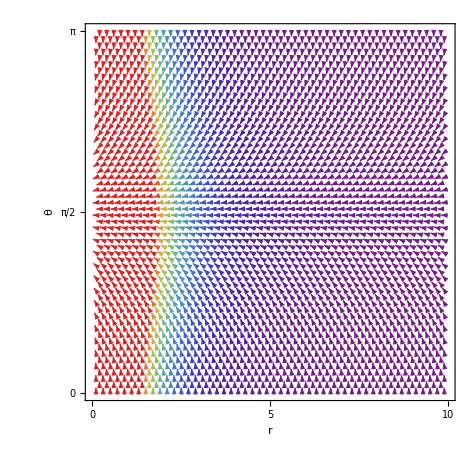

```mathematica
plvec=VectorPlot[B0* RE^3/r^3 {-2 Sin[θ],Cos[θ]},{r,0,10},{θ,0,Pi},PlotRange->All,Frame->True,FrameLabel->{"r","θ"},LabelStyle->{FontFamily->"Times New Roman",20},VectorPoints->50,VectorColorFunction->"Rainbow",FrameTicks->{{{-2Pi,-3Pi/2,-Pi/2,-Pi,0,Pi,3Pi/2,Pi/2,2Pi},{None,None}},{{-10,-5,0,5,10},{None,None}}}]
Export["plvec.png",Show[plvec,ImageSize->8 inches]];
```

```mathematica
Clear[RE,B0 ,me ,r,q,E0 ,BE ]
```

Υπολογίζουμε τη στροφή στις σφαιρικές συντεταγμένες και βλέπουμε ότι δεν χρειάζεται κάποια αλλαγή στο πεδίο, μιας και ισούται με 0.

```mathematica
Curl[B,{r,θ,ϕ},"Spherical"]
```

{0,0,0}

Λύνουμε τη διαφορική εξίσωση για να βρούμε τις πεδιακές γραμμές

```mathematica
sol= DSolve[r'[ θ ]/r[ θ ]== B[[1]]/B[[2]] ,r[ θ], θ]/.C[1] ->C
```

{{r[θ]→C Cos[θ]^2}}

Και τις σχεδιάζουμε για διάφορες τιμές της σταθεράς C

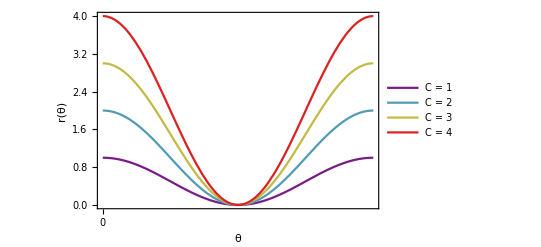

```mathematica
plr=Plot[Evaluate[Table[r[θ]/.sol,{C ,{1,2,3,4}}]],{θ,0,Pi},Frame->True,FrameLabel->{"θ","r(θ)"},FrameTicks->{{Automatic,{None,None}},{{-2Pi,-3Pi/2,-Pi/2,-Pi,0,Pi,3Pi/2,Pi/2,2Pi},{None,None}}},PlotLegends->{"C = 1","C = 2","C = 3","C = 4"},PlotStyle->"Rainbow"]
Export["plr.png",Show[plr,ImageSize->8 inches]];
```

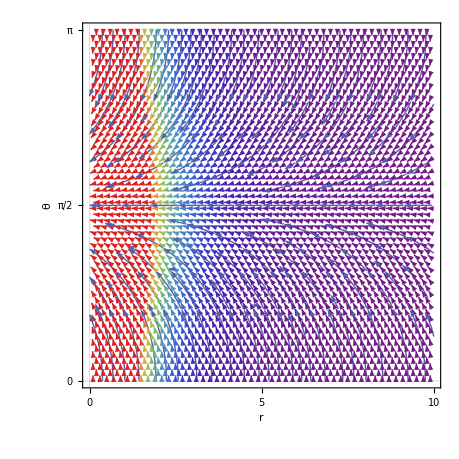

```mathematica
RE= 64*10^5;(*meters*)
B0 = 3*10^(-5);
me = 9.1093837*10^(-31) ; (* kg *)
r =2*RE; 
q=-1.6*10^(-19); (*Coulomb*)
E0 = 1.6021773*10^(-13);(*Joule*)(*13*)
BE = a//N;
strB=StreamPlot[B0* RE^3/r^3 {-2 Sin[θ],Cos[θ]},{r,0,10 },{θ,0,Pi},Frame->True,FrameLabel->{"r","θ"},VectorPoints->50,FrameTicks->{{{-2Pi,-3Pi/2,-Pi/2,-Pi,0,Pi,3Pi/2,Pi/2,2Pi},{None,None}},{{-10,-5,0,5,10},{None,None}}},LabelStyle->{FontFamily->"Times New Roman",20},VectorColorFunction->"Rainbow",PlotTheme->"Scientific"]
Export["strB.png",Show[strB,ImageSize->8 inches]];
```

```mathematica
Clear[RE,B0 ,me ,r,q,E0 ,BE ]
```

Έπειτα ορίζουμε το μαγνητικό πεδίο για θ =0 και αντικαθιστούμε το B_E

```mathematica
a=B[[2]]*r^3/. θ -> 0
```

B0 RE^3

```mathematica
Bdot=FullSimplify[B /.a -> BE]//N
```

{-(2. BE Sin[θ])/r^3,(BE Cos[θ])/r^3,0.}

το οποίο έχει μέτρο

```mathematica
Bdotmag = Sqrt[Sum[Bdot[[i]]^2,{i,1,3}]]
```

√(0.+(BE^2 Cos[θ]^2)/r^6+(4. BE^2 Sin[θ]^2)/r^6)

Αντικαθιστούμε τώρα το r(θ) του 1ου ερωτήματος στο μέτρο του Bdot

```mathematica
Bdotmagr = FullSimplify[Sqrt[Sum[Bdot[[i]]^2,{i,1,3}]]/.r-> sol[[1]][[1]][[2]],Assumptions->BE>0 && r>0]
```

BE √((Sec[θ]^10 (1.+4. Tan[θ]^2))/C^6)

και έτσι μελετάμε τη σχέση που προκύπτει, καταλήγοντας στο πίνακα

```mathematica
maxBdotmagr =Quiet[Table[FindMaximum[Evaluate[Table[Bdotmagr/BE ,{C,{1,2,3}}]][[i]],θ,AccuracyGoal->100,PrecisionGoal->100][[1]],{i,1,3}]];
maxtheta =Quiet[Table[FindMaximum[Evaluate[Table[Bdotmagr/BE ,{C,{1,2,3}}]][[i]],{θ,Pi/2},AccuracyGoal->100,PrecisionGoal->100][[2]][[1]][[2]],{i,1,3}]];
maxthetadeg=Mod[maxtheta/Degree,360];
Grid[{
{"C" ,"θ_max","B(θ_max)/BE" ,"B(0)/BE" },{1,maxthetadeg[[1]],maxBdotmagr[[1]],Bdotmagr/ BE/.θ->0 /.C->1},{2,maxthetadeg[[2]],maxBdotmagr[[2]],Bdotmagr/ BE/.θ->0 /.C->2},{3,maxthetadeg[[3]],maxBdotmagr[[3]],Bdotmagr/ BE/.θ->0 /.C->3}
},Frame->All]
```

C | θ_max | B(θ_max)/BE | B(0)/BE
1 | 90. | 1.76534×10^79 | 1.
2 | 90. | 2.20667×10^78 | 0.125
3 | 90. | 6.17489×10^77 | 0.037037

και το γράφημα

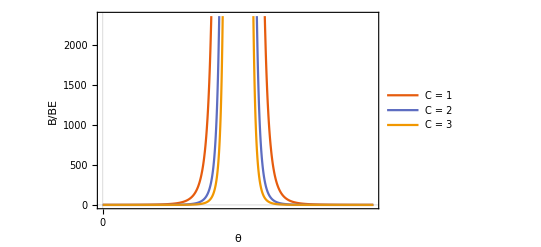

```mathematica
Brthetaplt=Plot[Evaluate[Table[Bdotmagr/BE ,{C,{1,2,3}}]],{θ,0,Pi},PlotTheme->"Scientific",PlotLegends->{"C = 1" ,"C = 2","C = 3"},Frame->True,FrameTicks->{{Automatic,{None,None}},{{-2Pi,-3Pi/2,-Pi/2,-Pi,0,Pi,3Pi/2,Pi/2,2Pi},{None,None}}},LabelStyle->{FontFamily->"Times New Roman",20},FrameLabel->{"θ","B/BE"}]
Export["Brthetaplt.png",Show[Brthetaplt,ImageSize->8 inches]];
```

Το γεωγραφικό πλάτος όπου ένα σωματίδιο ανακλάται βρίσκεται από τη σχέση

```mathematica
θt=Quiet[Solve[vvertical^2 /(BE)== (vparallel^2 + vvertical^2)/(√((1-θ^2/2)^2 BE^2+4. θ^2 BE^2)),θ]][[4]][[1]][[2]]; (* Umran p. 58 *)
Mod[θt/Degree,360]
```

36.3783

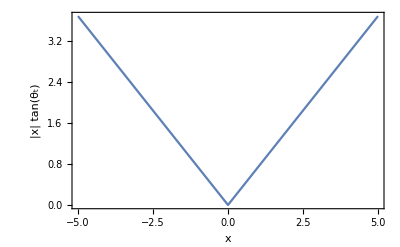

```mathematica
plttheta=Plot[Tan[θt]Abs[x],{x,-5,5},Frame->True,FrameLabel->{"x","|x| tan(θ_t)"},PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman",20},FrameTicks->None]
Export["plttheta.png",Show[plttheta,ImageSize->8 inches]];
```

Όπου αν δεν χρησιμοποιήσουμε ανάπτυγμα έχουμε ότι

```mathematica
Mod[Quiet[NSolve[Bdotmag == 3/2 BE/r^3 ,θ ]][[3]][[1]][[2]]/Degree,360]
```

40.203

Τώρα θα κατασκευάσουμε την ταχύτητα ολίσθησης, αρχικά υπολογίζουμε τη Gradient του πεδίου

```mathematica
FullSimplify[Grad[Bdotmag,{r,θ,ϕ},"Spherical"],Assumptions->r>0 && BE>0]/.θ->0
```

{-(3. BE)/r^4,0.,0.}

και το εξωτερικό γινόμενο του πεδίου επί το Gradient δια το μέτρο του πεδίου στη 3η

```mathematica
BcrossNablatoB3 = FullSimplify[ Cross[Bdot,Grad[Bdotmag,{r,θ,ϕ},"Spherical"]]/Bdotmag^3,Assumptions->r>0 &&BE>0]
```

{0.,0.,(r^2 (3.75 Cos[θ]-0.75 Cos[3 θ]))/(BE (2.5-1.5 Cos[2 θ])^2)}

εν τέλει έχουμε

```mathematica
v =FullSimplify[ (vparallel^2+1/2 *vvertical^2 )BcrossNablatoB3/(Abs[q]/me),Assumptions->r>0 &&BE>0&&q<0]
```

{0.,0.,(E0 r^2 (-2.22222 Cos[θ]+0.444444 Cos[3 θ]))/(BE q (1.66667-1. Cos[2 θ])^2)}

```mathematica
v/.θ->0
```

{0.,0.,-(4. E0 r^2)/(BE q)}

```mathematica
RE= 64*10^5;(*meters*)
B0 = 3*10^(-5);
me = 9.1093837*10^(-31) ; (* kg *)
r =2*RE; 
q=-1.6*10^(-19); (*Coulomb*)
E0 = 1.6021773*10^(-13);(*Joule*)(*13*)
BE = a//N;
```

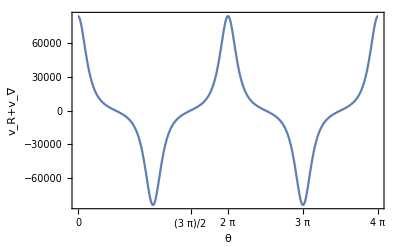

```mathematica
vplot=Plot[v[[3]],{θ, 0, 4Pi},Frame->True,FrameLabel->{"θ","v_R+v_∇"},PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman",20},FrameTicks->{{None,{None,None}},{{0,Pi,3Pi/2,Pi/2,2Pi,2Pi+Pi/2,2Pi+Pi,2Pi+3Pi/2,2Pi+2Pi},{None,None}}}]
Export["vplot.png",Show[vplot,ImageSize->8 inches]];
```

δηλαδή στον Ισημερινό

```mathematica
v/.θ->0
```

{0.,0.,83446.7}

```mathematica
Clear[RE,B0 ,me ,r,q,E0 ,BE ]
```

Υπολογίζουμε την ακτίνα Larmor

```mathematica
rl = me * vvertical/(Abs[q]*Sum[Sqrt[(B[[i]]/.θ->0)^2],{i,1,3}])/.r->2RE
```

(16 √E0 √me)/(√3 √(B0^2) Abs[q])

και το πηλίκο κλίσης του πεδίου προς το πεδίο

```mathematica
nablaBtoB=Abs[FullSimplify[Grad[Bdotmag,{r,θ,ϕ},"Spherical"]/Bdotmag,Assumptions->BE>0 && r>0]][[1]]/.θ -> 0
```

3./Abs[r]

και πολλαπλασιάζουμε για να δούμε αν είναι <<<1

```mathematica
ConditionCheck =rl*nablaBtoB
```

(27.7128 √E0 √me)/(√(B0^2) Abs[q] Abs[r])

Τέλος υπολογίζουμε το χρόνο που θα πάρει σε ένα σωματίδιο, να κάνει μια πλήρη περιστροφή

```mathematica
T = (2 Pi r)/v[[3]]/(3600)/.θ->0
```

-(0.000436332 BE q)/(E0 r)

```mathematica
RE= 64*10^5;(*meters*)
B0 = 3*10^(-5);
me = 9.1093837*10^(-31) ; (* kg *)
r =2*RE; 
q=-1.6*10^(-19); (*Coulomb*)
E0 = 1.6021773*10^(-13);(*Joule*)(*13*)
BE = a//N;
```

```mathematica
ConditionCheck
```

0.000172317

```mathematica
T
```

0.267718